## Lesson

~~ for sequence of string patterns:

```mathematica
StringCases["+string +patterns are +quite +easy","+"~~_]
```

{+s,+p,+q,+e}

Shortest sequence that matches pattern:

```mathematica
StringCases["now [several] important [words]","["~~Shortest[x__]~~"]"->Framed[x]]
```

{several,words}

Replace instances of pattern:

```mathematica
StringReplace["now [several] important [words]","["~~Shortest[x__]~~"]":>ToUpperCase[x]]
```

now SEVERAL important WORDS

Test if string matches pattern:

```mathematica
StringMatchQ["+e","+"~~_]
```

True

Pattern constructs matching different types of characters:

```mathematica
StringCases["12 and 123 and 4567 and x456",Whitespace~~LetterCharacter~~DigitCharacter..]
```

{ x456}

Split string into list of pieces:

```mathematica
StringSplit["The quick brown fox."]
```

{The,quick,brown,fox.}

Join list of strings together:

```mathematica
StringJoin[{"The","quick","brown","fox."}]
```

Thequickbrownfox.

Join list of strings together and inserting substring in between each:

```mathematica
StringRiffle[{"The","quick","brown","fox."},"+"]
```

The+quick+brown+fox.

Convert text to string:

```mathematica
Characters[TextString[abcde]]
```

{a,b,c,d,e}

Change string template based on slots ``:

```mathematica
StringTemplate["first `` then ``"][100,200]
```

first 100 then 200

Evaluate expression in <* *> of string template:

```mathematica
StringTemplate["the time now is <* Now *>"][]
```

the time now is Wed 2 Oct 2024 13:16:54

## Questions

Q1. Replace each space in “1 2 3 4” with “---“.

```mathematica
StringReplace["1 2 3 4",Whitespace->"---"]
```

1---2---3---4

Q2. Get a sorted list of all sequences of 4 digits (representing possible dates) in the Wikipedia article on computers.

```mathematica
Sort[StringCases[WikipediaData["computers"],DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter]]
```

{1000,1235,1357,1357,1595,1613,1620,1630,1640,1770,1822,1831,1833,1835,1872,1872,1876,1876,1888,1890,1897,1901,1901,1906,1914,1920,1920,1925,1927,1930,1934,1936,1936,1937,1938,1939,1940,1941,1941,1942,1943,1943,1943,1943,1944,1945,1945,1945,1945,1945,1945,1947,1947,1947,1948,1948,1949,1950,1950,1950,1950,1950,1951,1951,1952,1953,1953,1955,1955,1955,1955,1957,1958,1958,1959,1959,1960,1962,1964,1967,1968,1970,1970,1970,1970,1990,1998,2000,2000,2000,2016,2400,2468,4000,4004,5000,5100,6502,6510}

Q3. Extract “headings” in the Wikipedia article about computers, as indicated by strings starting and ending with “===”.

```mathematica
StringCases[WikipediaData["computers"],"=== "~~Shortest[x___]~~" ==="->x]
```

{Pre-20th century,First computer,Electromechanical calculating machine,Analog computers,Digital computers,Electromechanical,Vacuum tubes and digital electronic circuits,Modern computers,Concept of modern computer,Stored programs,Transistors,Integrated circuits,Mobile computers,By architecture,By size, form-factor and purpose,History of computing hardware,Other hardware topics,Input devices,Output devices,Control unit,Central processing unit (CPU),Arithmetic logic unit (ALU),Memory,Input/output (I/O),Multitasking,Multiprocessing,Languages,Programs,Stored program architecture,Machine code,Programming language,Low-level languages,High-level languages,Program design,Bugs,Computer architecture paradigms,Artificial intelligence}

Q4. Use a string template to make a grid of results of the form i+j=... for i and j up to 9.

```mathematica
Grid[Table[StringTemplate["`1`+`2`=`3`"][i,j,i+j],{i,9},{j,9}]]
```

1+1=2 | 1+2=3 | 1+3=4 | 1+4=5 | 1+5=6 | 1+6=7 | 1+7=8 | 1+8=9 | 1+9=10
2+1=3 | 2+2=4 | 2+3=5 | 2+4=6 | 2+5=7 | 2+6=8 | 2+7=9 | 2+8=10 | 2+9=11
3+1=4 | 3+2=5 | 3+3=6 | 3+4=7 | 3+5=8 | 3+6=9 | 3+7=10 | 3+8=11 | 3+9=12
4+1=5 | 4+2=6 | 4+3=7 | 4+4=8 | 4+5=9 | 4+6=10 | 4+7=11 | 4+8=12 | 4+9=13
5+1=6 | 5+2=7 | 5+3=8 | 5+4=9 | 5+5=10 | 5+6=11 | 5+7=12 | 5+8=13 | 5+9=14
6+1=7 | 6+2=8 | 6+3=9 | 6+4=10 | 6+5=11 | 6+6=12 | 6+7=13 | 6+8=14 | 6+9=15
7+1=8 | 7+2=9 | 7+3=10 | 7+4=11 | 7+5=12 | 7+6=13 | 7+7=14 | 7+8=15 | 7+9=16
8+1=9 | 8+2=10 | 8+3=11 | 8+4=12 | 8+5=13 | 8+6=14 | 8+7=15 | 8+8=16 | 8+9=17
9+1=10 | 9+2=11 | 9+3=12 | 9+4=13 | 9+5=14 | 9+6=15 | 9+7=16 | 9+8=17 | 9+9=18

Q5. Find names of integers below 50 that have an “i” somewhere before an “e”.

```mathematica
Select[IntegerName[Range[49]],StringMatchQ[#,___~~"i"~~___~~"e"~~___]&]
```

{five,nine,thirteen,fifteen,sixteen,eighteen,nineteen,twenty-five,twenty-nine,thirty-one,thirty-three,thirty-five,thirty-seven,thirty-eight,thirty-nine,forty-five,forty-nine}

Q6. Make any 2-letter word uppercase in the first sentence from the Wikipedia article on computers.

```mathematica
StringReplace[TextSentences[WikipediaData["computers"]][[1]],x:(Whitespace~~LetterCharacter~~LetterCharacter~~Whitespace):>ToUpperCase[x]]
```

A computer IS a machine that can BE programmed TO automatically carry out sequences OF arithmetic OR logical operations (computation).

Q7. Make a labeled bar chart of the number of countries whose TextString names start with each possible letter.

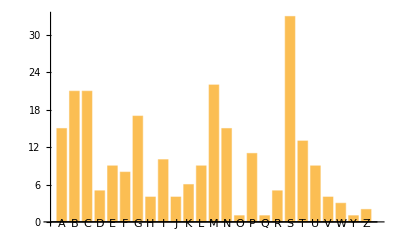

```mathematica
BarChart[Counts[StringTake[CommonName[EntityList[EntityClass["Country","Countries"]]],1]],ChartLabels->Automatic]
```

Q8. Find simpler code for Grid[Table[StringJoin[TextString[i], “^”, TextString[j], “=”, TextString[i^j]], {i, 5}, {j, 5}]].

```mathematica
Grid[Table[StringTemplate["`1`^`2`=`3`"][i,j,i^j],{i,5},{j,5}]]
```

1^1=1 | 1^2=1 | 1^3=1 | 1^4=1 | 1^5=1
2^1=2 | 2^2=4 | 2^3=8 | 2^4=16 | 2^5=32
3^1=3 | 3^2=9 | 3^3=27 | 3^4=81 | 3^5=243
4^1=4 | 4^2=16 | 4^3=64 | 4^4=256 | 4^5=1024
5^1=5 | 5^2=25 | 5^3=125 | 5^4=625 | 5^5=3125